```mathematica
W=k (4 π M (BesselK[0,k] D[BesselI[0,k],k])/(BesselI[0,k] D[BesselK[0,k],k] Subscript[μ, 2]-BesselK[0,k] D[BesselK[0,k],k] Subscript[μ, 1])+(k^2-1)D[BesselI[0,k],k]/BesselI[0,k])
```

k (((-1+k^2) BesselI[1,k])/BesselI[0,k]+(4 M π BesselI[1,k] BesselK[0,k])/(BesselK[0,k] BesselK[1,k] μ_1-BesselI[0,k] BesselK[1,k] μ_2))

```mathematica
Manipulate[Plot[y (((-1+y^2) BesselI[1,y])/BesselI[0,y]+(4 M π y BesselI[1,y] BesselK[0,y])/(BesselK[0,y] BesselK[1,y] Subscript[μ, 1]-BesselI[0,y] BesselK[1,y] Subscript[μ, 2])),{y,0,3},PlotRange-> {{0,2},{-10,10}}],{M,0,20},{Subscript[μ, 1],1,10},{Subscript[μ, 2],1,10}]
```

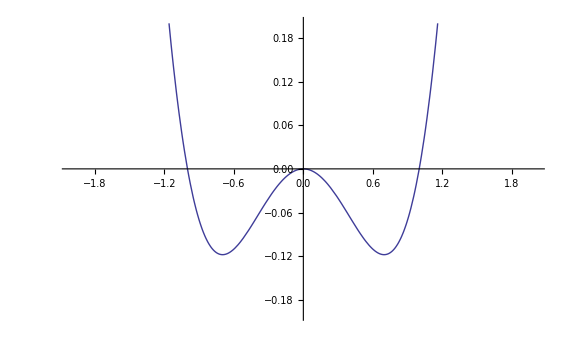

```mathematica
Plot[(x (-1+x^2) BesselI[1,x])/BesselI[0,x],{x,-4.645102253320389,4.645102253320389},PlotRange-> {{-2,2},{-0.2,0.2}}]
```

```mathematica
D[BesselI[1,k],k]/.k->0
```

1/2

```mathematica
Manipulate[Plot[D[BesselI[1,k],k],{k,1,20},PlotRange->{{-15,15},{-2,2}}],{k,0,10}}]
```

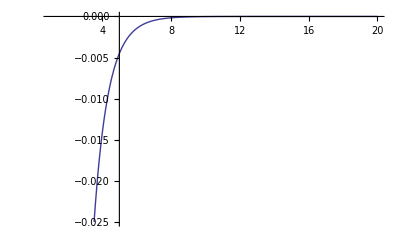

```mathematica
Plot[1/2 (-BesselK[0,k]-BesselK[2,k]),{k,1,20}]
```

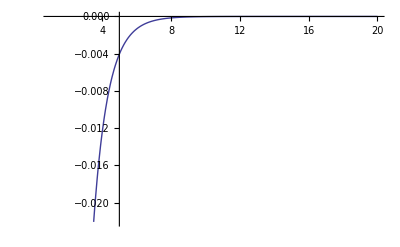

```mathematica
Plot[-BesselK[1,k],{k,1,20}]
```